```mathematica
Φ[σ_,  μ1_, μ2_, Y1_, Y2_]:=  2r - σ(μ1 Abs[r  - Y1]- μ2 Abs[r + Y2] );
```

```mathematica
F[13] = Φ[-1,600,599.5,600,-1];
```

```mathematica
(-F[13] /.r->-1) - (-F[13] /.r->-8)
```

-17.5

```mathematica
Table[i[[1]], {i, {{10,9},{2,9}}}]
```

{10,2}

```mathematica
-F[13] /.r->12132-(-F[13] /.r->12000)
```

494437.

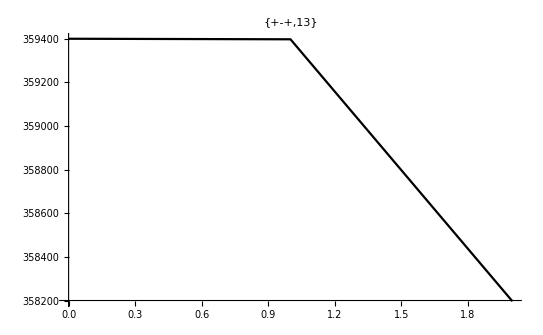
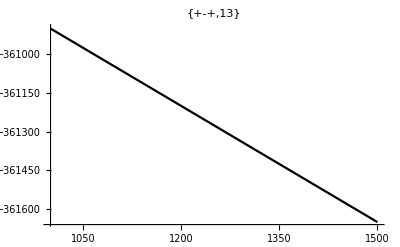
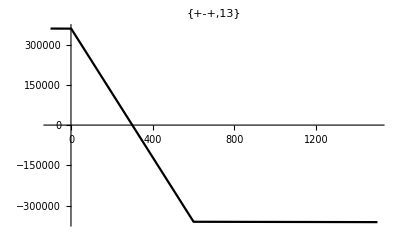

```mathematica
Table[Plot[- F[13],{r,point[[1]],point[[2]]},PlotLabel->{labels[[13]] , 13},PlotRange->All,PlotStyle->Black], {point,{{ 0, 2},{1000, 1500},{-100, 1500}}}]
```

```mathematica
Manipulate[
Show[
Plot[-Φ[σ,  μ1, μ2, Y1, Y2],{r,0,20}],
Plot[μ2 Abs[r+ Y2],{r,0,20}, PlotStyle->Yellow],
Plot[-μ1 Abs[r- Y1],{r,0,20}, PlotStyle->Red]
], {μ1, -40, 40}, {σ,-1,1},{μ2, -40, 40}, {Y1, -5, 5 },  {Y2, -5, 5 }]
```

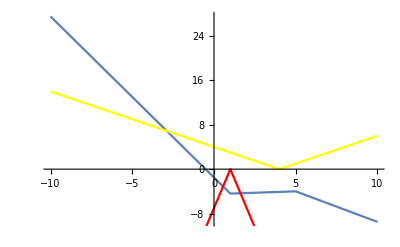

```mathematica
Show[Plot[-Φ[-1,1.5, 0.6 , 1, -5],{r,-10,10}],
Plot[1 Abs[r-4],{r,-10,10}, PlotStyle->Yellow],
Plot[-7  Abs[r- 1],{r,-10,10}, PlotStyle->Red]]
```